```mathematica
boat = ImplicitRegion[x^2/4<y<2 && -2 < x<2&&0<y<2 && -5 < z <5, {x,y, z}];
mass = NIntegrate[300, {x,y, z}∈boat]+5000;
xcom = N[1/mass*Integrate[300*x, {x,y,z}∈boat],10];
zcom = N[1/mass*Integrate[300*z, {x,y,z}∈boat],10];
ycom = N[ 1/mass*Integrate[300*y, {x,y,z}∈boat],10];
com = {xcom,ycom,zcom};
fgrav = -(mass * 9.8);
fbuoy = -fgrav;
displaced = N[fgrav/(1000*9.8),10];
Momentarm[theta_]:=(
(* Returns the moment of the boat
theta_: the heel angle in degrees *)
water = ImplicitRegion[0<y<Tan[theta]*x+d&&-2<x<2&&0<y<2 && -5<z<5,{x,y, z}];
under = RegionIntersection[boat,water];
disp = Integrate[1000, {x,y,z}∈under, Assumptions->{0<d<2}];
maxdisp = disp/.{d->2};
waterline =NSolve[disp==mass,d,Reals];
draft = N[d /. waterline[[1]],5];
cob = RegionCentroid[under/.{d->draft}];
moment =N[(cob-com)×{fbuoy*Sin[theta],fbuoy*Cos[theta],0},3];
moment[[3]]
)
```

```mathematica
Momentarm[70°]
```

52366.

```mathematica
avstable = {Parallelize[Table[Momentarm[angle Degree],{angle,0,150}]]};
```

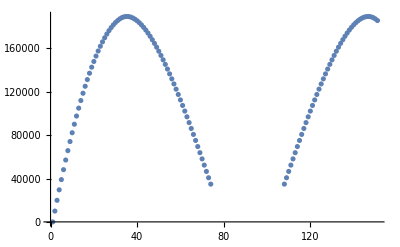

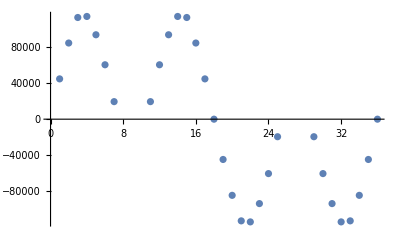

```mathematica
ListPlot[avstable, AxesLabel->Automatic]
```